# Teoría de Autómatas y Lenguajes Formales

## Clase 11 - Máquinas de Turing

Profesor: Tomás de Camino Beck, Ph.D.

tomas.decamino@gmail.com

## Introducción

Utilicemos el último teorema de Fermat para explicar como hay programas que no sabemos que se detienen. El teorema de Fermat dice que dado ,  no existe solución para  para . Construyamos primero una función para crear tripletas para evaluar numéricamente,

```mathematica
tripleta[n_]:=Flatten[Table[{n-i-j, i ,j},{j,1,n-2},{i,1,n-j-1}],1]
```

```mathematica
tripleta[4]
```

{{2,1,1},{1,2,1},{1,1,2}}

Ahora definimos una función para evaluar si la identidad es verdadera, para un valor determinado de  y

```mathematica
fermatTest[{x_,y_,z_},n_]:=z^n==x^n+y^n
```

```mathematica
fermatTest[{3,4,5},1]
```

False

Podemos evaluar ahora para un conjunto de tripletas,

```mathematica
fermatTest[#,1]&/@tripleta[8]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,False,False,False}

ahora construimos una función para determinar si hay al menos una tripleta que es verdadera,

```mathematica
solutionQ[n_,power_]:=MemberQ[fermatTest[#,power]&/@tripleta[n], True]
```

Ejemplos:

```mathematica
solutionQ[12,1]
```

True

```mathematica
solutionQ[12,2]
```

True

Ahora construimos este ciclo que evalúa  para diferentes vales de potencia,

```mathematica
n=1;
power = 2;
While[True,
If[solutionQ[n,power],
Print["Hello World!"];
Break[]];
n++]
```

Hello World!

Cuando se detiene imprime “Hello World!”, podremos probar para potencias de 3? (no lo hagan o se les va a quedar el ciclo sin parar).

Este ejemplo ilustra de manera intuitiva la dificultad de determinar si un programa se detiene y da un resultado. Existirá un programa o función que me permita decir si un programa se detiene o no?

## Máquina de Turing

Una máquina de turing se define como , donde,

es un conjunto finito de estados

es un conjunto finito de símbolos de entrada

es un conjunto de símbolos de cinta.

función de transición , con ,  y  representa los movimiento a la derecha  o izquierda ()

estado inicial

símbolo de espacio en blanco

conjunto de estados finales

## Ejemplo de uso de MT en Mathematica

Consideremos la MT del libro de Hopcroft (pg 273),

La definición de la función de transición en Mathematica la realizamos con reglas, con una notación muy similar a la de Hopcroft, es decir . En Mathematica las direcciones son , y . Para el ejemplo del cuadro entonces tenemos,

```mathematica
rules={
{0,"0"}-> {1,"X",1},
{0,"Y"}-> {3,"Y",1},
{1,"0"}-> {1,"0",1},
{1,"1"}-> {2,"Y",-1},
{1,"Y"}-> {1,"Y",1},
{2,"0"}-> {2,"0",-1},
{2,"X"}-> {0,"X",1},
{2,"Y"}-> {2,"Y",-1},
{3,"Y"}-> {3,"Y",1},
{3,"B"}-> {4,"B",1}
};
```

Para ejecutar la máquina utilizamos la función TuringMachinepaclet:ref/TuringMachine[rule,init,t]. En init utilizamos {s,{{a_1,a_2,…},0}}, para inicializar en estado  con la cinta {a_1,a_2,…}, y el 0 indica que utilizaremos una cinta infinita (no da error si nos movemos más allá de la cinta de inicio),

```mathematica
evolution=TuringMachine[rules,{0,{{"0","0","1","1","B","B","B"},0}},15]
```

{{{0,1,0},{0,0,1,1,B,B,B}},{{1,2,1},{X,0,1,1,B,B,B}},{{1,3,2},{X,0,1,1,B,B,B}},{{2,2,1},{X,0,Y,1,B,B,B}},{{2,1,0},{X,0,Y,1,B,B,B}},{{0,2,1},{X,0,Y,1,B,B,B}},{{1,3,2},{X,X,Y,1,B,B,B}},{{1,4,3},{X,X,Y,1,B,B,B}},{{2,3,2},{X,X,Y,Y,B,B,B}},{{2,2,1},{X,X,Y,Y,B,B,B}},{{0,3,2},{X,X,Y,Y,B,B,B}},{{3,4,3},{X,X,Y,Y,B,B,B}},{{3,5,4},{X,X,Y,Y,B,B,B}},{{4,6,5},{X,X,Y,Y,B,B,B}},{{4,6,5},{X,X,Y,Y,B,B,B}},{{4,6,5},{X,X,Y,Y,B,B,B}}}

El resultado es , donde estado  de la cabeza,  posición  de la cabeza, y posición   desde el inicio.

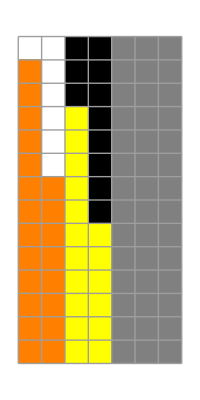

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"1"->Black,"0"->White,"X"->Orange,"Y"->Yellow,"B"->Gray},Mesh->True]
```

Podemos utilizar ListAnimate para animar paso a paso la evaluación sobre la cinta.

```mathematica
ListAnimate[Last/@evolution]
```

## Busy Beaver

Un juego de Busy Beavebusy consiste en diseñar una Máquina de Turing que se detenga, con sólo do símboles y un número determinado de estados. Un BB escribe 1s en la cinta que normalmente tiene 0s, y tiene un estado en el que se detiene el BB. Este es una ejemplo de uno con 4 estados.

```mathematica
rules={
{0,0}-> {1,1,1},
{0,1}-> {1,1,-1},
{1,0}-> {0,1,-1},
{1,1}-> {2,0,-1},
{2,0}-> {4,1,1},
{2,1}-> {3,1,-1},
{3,0}-> {3,1,1},
{3,1}-> {0,0,1}
};
```

```mathematica
busy=TuringMachine[rules,{{0,11},{{},0}},107];
```

```mathematica
busy[[1]]
```

{{0,11,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

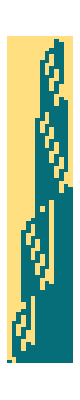

```mathematica
ArrayPlot[Last /@busy]
```

Determinar si un BB se detiene es indecidible, es decir no se puede construir un algoritmo que determine si se va a detener (o cuando se va a detener)